```mathematica
f[x_,h_,r_] = h+ x*(r-x);
rangeMin = -10;
rangeMax = 10;
ContourPlot3D[f[x,h,r] == 0, {x,rangeMin, rangeMax},{h,rangeMin, rangeMax},{r,rangeMin, rangeMax}, AxesLabel->{x,h,r}]
```

-Graphics3D-

```mathematica
(* find xstar*)
```

```mathematica
xstar = Solve[f[x,h,r]==0, x]
xstar1[h_,r_] = xstar[[1]];
xstar2[h_,r_] = xstar[[2]];
(* FPs *)
```

{{x→1/2 (r-√(4 h+r^2))},{x→1/2 (r+√(4 h+r^2))}}

```mathematica
(* Eval *)
```

```mathematica
sol1 = D[f[x,h,r],x]
sol2[] = Solve[sol1==0,x]
sol2[r_] = r/2
sol3 = f[x,h,r]/.sol2
sol31 = f[x,h,r]/.sol1
(*sol4[r_] = Solve[sol3==0,h];
sol5[r_] = Solve[sol31==0,h];
pl1 = Plot[sol4[[r]], {r,-10,10}];
*)
```

r-2 x

{{x→r/2}}

r/2

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

h+(r-x) x/.sol2

ReplaceAll::reps: {r-2 x} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

h+(r-x) x/.r-2 x

-r^2/4

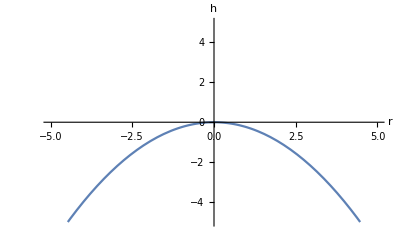

```mathematica
h[r_] = -r^2/4
Plot[h[r], {r,-5,5}, PlotRange->{{-5,5},{-5,5}}, AxesLabel->{r,h}]
```

```mathematica
-Graphics-
(* Where and how many FPs determined in PDF sketch *)
```

```mathematica
(* stability of FPs *)
```

```mathematica
Manipulate[Plot[h+ x*(r-x),{x,-2,2}],{r,-2,2}, {h,-2,2}]
```